{100000.,{4.09379×10^-26,1.26283×10^-25,3.47021×10^-25,6.69043×10^-25,2.68771×10^-25,0.}}

{0,0.01,0.0251189,0.0630957,0.158489,0.398107,1.,2.51189,6.30957,15.8489,39.8107,100.}

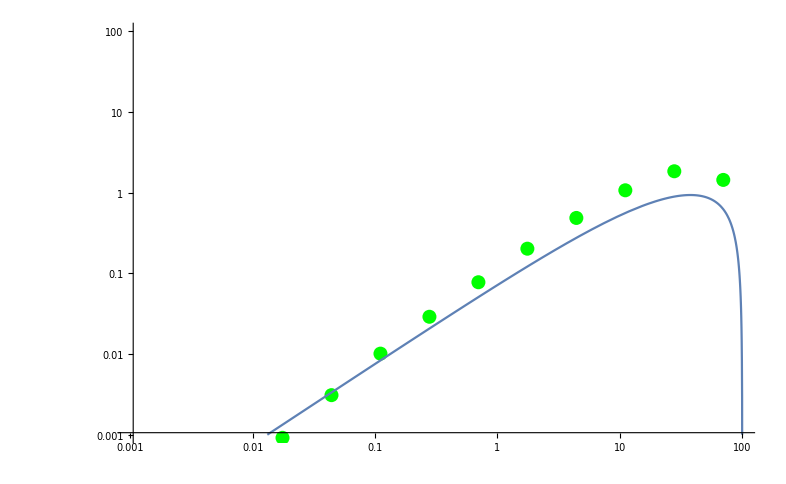

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["specout4e","TSV"];
eflux=Import["specraw4e"]//ToExpression
tab=Flatten[tab,1]//ToExpression(*Imports photon spectrum for nevents in TeV*);
nevents=100000;
au=1.49598 10^11 *100;(*distance from earth to sun in cm*)
aum=1.49598 10^11 ;(*distance from earth to sun in m*)
SR=6.957 10^8;(*Solar radius in m*)
(*annin=Import["ann","Table"]//ToExpression;*)
(*annrate=eflux[[5]](*DM annihilation rate per second*);*)
minbin=0.01;
maxbin=100.;
bincount=10;
maxheight=5 10^-11;
(*weights=Table[(tab[[i]])^2/nevents annrate/(4 π au^2),{i,1,Length[tab]}];*)
(*wtab=WeightedData[tab,weights];
Histogram[wtab,{"Log",bincount},"LogCount",PlotRange-> {{minbin,maxbin},{0,maxheight}}]*)
bins=Prepend[Table[10^li,{li,Log10[minbin],Log10[maxbin],(Log10[maxbin]-Log10[minbin])/bincount}],0]

(*bins={0.,0.5,1.6,5.0,15.7,50.0,158.1};*)
f[in_]:=Table[in>bins[[i]],{i,1,Length[bins]}];
tabsplit=SplitBy[tab,f[#]&];
dNdx0[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1)(*x0 is 2*E0/m1, ϵf is 2 mf / m1, where E0 is energy of photon in rest frame of mediator 1 and m1 is mass of mediator 1*);
dNdx1[x1_,ϵ1_,ϵf_]:=(t1max=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1min=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0[x0,ϵf],{x0,t1min,t1max}])(*ϵ1 is 2 m1/m2 where m2 is the dark matter mass?, x1 = E1/m2 where E1 is the photon energy in the rest frame of dm. See end of pg 3 in 1503.01773*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA]
dNdE1μ[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*105.66 10^-6(*TeV*))/mA]
E2dNdE1e[En_,mχ_,mA_]:=En^2 dNdE1e[En,mχ,mA]
E2dNdE1μ[En_,mχ_,mA_]:=En^2 dNdE1μ[En,mχ,mA]
E2dNdE1tot[En_,mχ_,mA_]:=1. En^2 dNdE1e[En,mχ,mA]+0. En^2 dNdE1μ[En,mχ,mA]
(*Show[{LogLogPlot[E2dNdE1e[En,50.,0.5 10^-3],{En,0.01,100}],LogLogPlot[E2dNdE1μ[En,50.,0.5 10^-3],{En,0.01,100},PlotStyle->Red]}]*)
(*widthread=eflux[[9]]
τ=ℏ/(widthread (*GeV*) 10^9(*eV/GeV*))/.{ℏ-> 4.135667662 10^-15(*eV s*)};
γ=eflux[[1]]/eflux[[2]];
vel=c √(1-1/γ^2)/.{c-> 3 10^8(*m/s*)};
Pr[d_]:=Exp[-d/( vel γ τ )](*Probability it has survived by distance d*);
Prdetect=Pr[SR]-Pr[aum](*How many decay between the surface of the sun and the distance to earth*);*)
dlogE=(Log10[maxbin]-Log10[minbin])/bincount;
en[j_]:=(bins⟦j⟧+bins⟦j+1⟧)/2;
EdN[j_]:=Sum[tabsplit[[j,i]],{i,1,Length[tabsplit⟦j⟧]}];
binnedtab=Table[{en[j],1/nevents EdN[j]/dlogE},{j,1,Length[tabsplit]}];
(*binnedtab=Table[{(bins⟦j⟧+bins⟦j+1⟧)/2,(1(*annrate*))/nevents(*1/(4π au^2)*) Sum[tabsplit[[j,i]],{i,1,Length[tabsplit⟦j⟧]}]},{j,1,Length[tabsplit]}];*)
HAWC=Log[{{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.0,8.1 10^-14},{50.0,158.1,6.3 10^-14}}];
HAWCbinned=Table[{(Exp[HAWC[[i,2]]]+Exp[HAWC[[i,1]]])/2,eflux[[2,i]]/((*Prdetect *)nevents)},{i,1,5}];
HAWCLines=Table[{Red,Thick,Line[{{HAWC⟦i,1⟧,HAWC⟦i,3⟧},{HAWC⟦i,2⟧,HAWC⟦i,3⟧}}]},{i,1,Length[HAWC]}];
ListLogLogPlot[(*{*)binnedtab(*,HAWCbinned}*),PlotStyle-> {Blue,Green},PlotRange-> (*Automatic*){{0.001,100.},{0.001,100.}} (*{{minbin,maxbin},{10^-19,maxheight}},Epilog-> HAWCLines*)];
Show[%,LogLogPlot[(*annrate*)(*1/(4π au^2)*)E2dNdE1tot[En,100.,0.05 10^-3],{En,0.001,100.},PlotRange-> (*Automatic*){{0.001,100.},{0.001,100.}}(*{{minbin,maxbin},{0.0005,1.5}}*)]]

(*Show[%,LogLogPlot[E2dNdE[En,50.],{En,0.01,100}],PlotRange->All]*)
```

```mathematica
binnedtab
```

{{0.005,0.00196442},{0.0149763,0.00208636},{0.0298817,0.00424094},{0.0596218,0.00876896},{0.118961,0.0156756},{0.237359,0.0296721},{0.473593,0.0580634},{0.944941,0.106199},{1.88541,0.136355},{3.76188,0.219772},{7.50594,0.130496}}

```mathematica
photonenergies=Table[]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table[]

```mathematica
Log10[{500.,1600.,5000.,15700.,50000.,158100.}]
%[[6]]-%[[5]]
```

{2.69897,3.20412,3.69897,4.1959,4.69897,5.19893}

0.499962

```mathematica
Log10[{0.5,1.6,5.0,15.7,50.,158.1}]
%[[6]]-%[[5]]
```

{-0.30103,0.20412,0.69897,1.1959,1.69897,2.19893}

0.499962